```mathematica
Get[FileNameJoin[{NotebookDirectory[], "functions.m"}]]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"];
b2 = MergeDirections["2_Ashwood_RGU.txt", "2_RGU_Ashwood.txt"];
b3 = MergeDirections["3_Cove_Mastrick.txt", "3_Mastrick_Cove.txt"];
b11 = MergeDirections["11_Northfield_Woodend.txt", "11_Woodend_Northfield.txt"];
b12 = MergeDirections["12_Heathryfold_Torry.txt", "12_Torry_Heathryfold.txt"];
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"];
b15 = MergeDirections["15_Balnagask_Circle_Countesswells.txt", "15_Countesswells_Balnagask_Circle.txt"];
b17 = MergeDirections["17_Dyce_Faulds_Gate.txt", "17_Faulds_Gate_Dyce.txt"];
b18 = MergeDirections["18_Dyce_Redmoss.txt", "18_Redmoss_Dyce.txt"];
b19 = MergeDirections["19_Culter_Tillydrone.txt", "19_Tillydrone_Culter.txt"];
b20 = MergeDirections["20_Guild_str_Hillhead.txt", "20_Hillhead_Guild_str.txt"];
b23 = MergeDirections["23_Raasay_Gardens_Heathryfold.txt",  "23_Heathryfold_Raasay_Gardens.txt"];
```

```mathematica
buses = {b1, b3, b11, b12, b13, b15, b17, b18, b19, b20, b23};
routeNames = {"1", "3", "11", "12", "13", "15", "17", "18", "19", "20", "23"};
```

```mathematica
TAPs=Algorithm821[buses, routeNames, Quantity[15, "Minutes"]];
```

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]]; 
(* This is the matrix we obtained for our model. Import it for quicker evaluation. *)
(*mtx = ImportMaxPlusMatrix["matrix_ct15"]*)
```

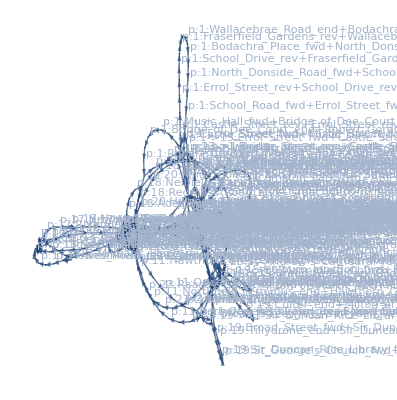

```mathematica
CreatePetriNetFromTAPs[TAPs]
```

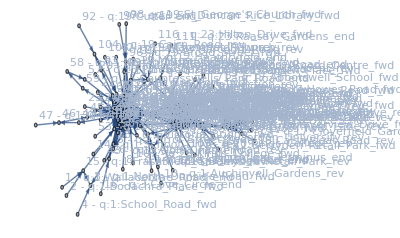

```mathematica
MakeAdjacencyGraph[mtx, TAPs]
```

```mathematica
v = MakeStateVector[mtx]
```

{-∞,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,-∞,0,0,-∞,0,-∞,0,0,-∞,0,0,-∞,-∞,0,-∞,0,0,0,-∞,-∞,0,0,0,-∞,0,0,0,-∞,0,-∞,0,-∞,0,0,0,0,0,-∞,0,-∞,-∞,0,-∞,0,0,-∞,0,-∞,0,0,-∞,-∞,0,-∞,0,-∞,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,0,0,-∞,-∞,0,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,0,0,-∞,0,-∞,0}

```mathematica
Count[v, 0] (* Number of buses *)
```

70

```mathematica
ttb = TimeTable[mtx,v, TAPs[[1]], 10];
```

```mathematica
routes = SplitByRoutes[ttb, routeNames];
```

```mathematica
ConvertToHoursTimetable[routes[[1]]] // MatrixForm
```

(q:1:Wallacebrae_Road_end | 06:13:00GMT+1TimeObject[{6,13,0},Instant,1.] | 06:25:00GMT+1TimeObject[{6,25,0},Instant,1.] | 07:07:00GMT+1TimeObject[{7,7,0},Instant,1.] | 07:37:00GMT+1TimeObject[{7,37,0},Instant,1.] | 08:11:00GMT+1TimeObject[{8,11,0},Instant,1.] | 08:41:00GMT+1TimeObject[{8,41,0},Instant,1.] | 09:15:00GMT+1TimeObject[{9,15,0},Instant,1.] | 09:45:00GMT+1TimeObject[{9,45,0},Instant,1.] | 10:19:00GMT+1TimeObject[{10,19,0},Instant,1.]
q:1:Bodachra_Place_fwd | 06:20:00GMT+1TimeObject[{6,20,0},Instant,1.] | 06:32:00GMT+1TimeObject[{6,32,0},Instant,1.] | 07:14:00GMT+1TimeObject[{7,14,0},Instant,1.] | 07:44:00GMT+1TimeObject[{7,44,0},Instant,1.] | 08:18:00GMT+1TimeObject[{8,18,0},Instant,1.] | 08:48:00GMT+1TimeObject[{8,48,0},Instant,1.] | 09:22:00GMT+1TimeObject[{9,22,0},Instant,1.] | 09:52:00GMT+1TimeObject[{9,52,0},Instant,1.] | 10:26:00GMT+1TimeObject[{10,26,0},Instant,1.]
q:1:North_Donside_Road_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:27:00GMT+1TimeObject[{6,27,0},Instant,1.] | 06:39:00GMT+1TimeObject[{6,39,0},Instant,1.] | 07:21:00GMT+1TimeObject[{7,21,0},Instant,1.] | 07:51:00GMT+1TimeObject[{7,51,0},Instant,1.] | 08:25:00GMT+1TimeObject[{8,25,0},Instant,1.] | 08:55:00GMT+1TimeObject[{8,55,0},Instant,1.] | 09:29:00GMT+1TimeObject[{9,29,0},Instant,1.] | 09:59:00GMT+1TimeObject[{9,59,0},Instant,1.]
q:1:School_Road_fwd | 06:07:00GMT+1TimeObject[{6,7,0},Instant,1.] | 06:34:00GMT+1TimeObject[{6,34,0},Instant,1.] | 06:46:00GMT+1TimeObject[{6,46,0},Instant,1.] | 07:28:00GMT+1TimeObject[{7,28,0},Instant,1.] | 07:58:00GMT+1TimeObject[{7,58,0},Instant,1.] | 08:32:00GMT+1TimeObject[{8,32,0},Instant,1.] | 09:02:00GMT+1TimeObject[{9,2,0},Instant,1.] | 09:36:00GMT+1TimeObject[{9,36,0},Instant,1.] | 10:06:00GMT+1TimeObject[{10,6,0},Instant,1.]
q:1:Errol_Street_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:12:00GMT+1TimeObject[{6,12,0},Instant,1.] | 06:39:00GMT+1TimeObject[{6,39,0},Instant,1.] | 06:51:00GMT+1TimeObject[{6,51,0},Instant,1.] | 07:33:00GMT+1TimeObject[{7,33,0},Instant,1.] | 08:03:00GMT+1TimeObject[{8,3,0},Instant,1.] | 08:37:00GMT+1TimeObject[{8,37,0},Instant,1.] | 09:07:00GMT+1TimeObject[{9,7,0},Instant,1.] | 09:41:00GMT+1TimeObject[{9,41,0},Instant,1.]
q:1:Castle_Street_fwd | 06:38:00GMT+1TimeObject[{6,38,0},Instant,1.] | 07:08:00GMT+1TimeObject[{7,8,0},Instant,1.] | 07:42:00GMT+1TimeObject[{7,42,0},Instant,1.] | 08:12:00GMT+1TimeObject[{8,12,0},Instant,1.] | 08:46:00GMT+1TimeObject[{8,46,0},Instant,1.] | 09:16:00GMT+1TimeObject[{9,16,0},Instant,1.] | 09:50:00GMT+1TimeObject[{9,50,0},Instant,1.] | 10:20:00GMT+1TimeObject[{10,20,0},Instant,1.] | 10:54:00GMT+1TimeObject[{10,54,0},Instant,1.]
q:1:Music_Hall_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:43:00GMT+1TimeObject[{6,43,0},Instant,1.] | 07:13:00GMT+1TimeObject[{7,13,0},Instant,1.] | 07:47:00GMT+1TimeObject[{7,47,0},Instant,1.] | 08:17:00GMT+1TimeObject[{8,17,0},Instant,1.] | 08:51:00GMT+1TimeObject[{8,51,0},Instant,1.] | 09:21:00GMT+1TimeObject[{9,21,0},Instant,1.] | 09:55:00GMT+1TimeObject[{9,55,0},Instant,1.] | 10:25:00GMT+1TimeObject[{10,25,0},Instant,1.]
q:1:Bridge_of_Dee_Court_end | 06:14:00GMT+1TimeObject[{6,14,0},Instant,1.] | 06:57:00GMT+1TimeObject[{6,57,0},Instant,1.] | 07:27:00GMT+1TimeObject[{7,27,0},Instant,1.] | 08:01:00GMT+1TimeObject[{8,1,0},Instant,1.] | 08:31:00GMT+1TimeObject[{8,31,0},Instant,1.] | 09:05:00GMT+1TimeObject[{9,5,0},Instant,1.] | 09:35:00GMT+1TimeObject[{9,35,0},Instant,1.] | 10:09:00GMT+1TimeObject[{10,9,0},Instant,1.] | 10:39:00GMT+1TimeObject[{10,39,0},Instant,1.]
q:1:Robert_Gordon_University_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:18:00GMT+1TimeObject[{6,18,0},Instant,1.] | 07:01:00GMT+1TimeObject[{7,1,0},Instant,1.] | 07:31:00GMT+1TimeObject[{7,31,0},Instant,1.] | 08:05:00GMT+1TimeObject[{8,5,0},Instant,1.] | 08:35:00GMT+1TimeObject[{8,35,0},Instant,1.] | 09:09:00GMT+1TimeObject[{9,9,0},Instant,1.] | 09:39:00GMT+1TimeObject[{9,39,0},Instant,1.] | 10:13:00GMT+1TimeObject[{10,13,0},Instant,1.]
q:1:Auchinyell_Gardens_rev | 06:08:00GMT+1TimeObject[{6,8,0},Instant,1.] | 06:26:00GMT+1TimeObject[{6,26,0},Instant,1.] | 07:09:00GMT+1TimeObject[{7,9,0},Instant,1.] | 07:39:00GMT+1TimeObject[{7,39,0},Instant,1.] | 08:13:00GMT+1TimeObject[{8,13,0},Instant,1.] | 08:43:00GMT+1TimeObject[{8,43,0},Instant,1.] | 09:17:00GMT+1TimeObject[{9,17,0},Instant,1.] | 09:47:00GMT+1TimeObject[{9,47,0},Instant,1.] | 10:21:00GMT+1TimeObject[{10,21,0},Instant,1.]
q:1:Great_Western_Road_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:23:00GMT+1TimeObject[{6,23,0},Instant,1.] | 06:34:00GMT+1TimeObject[{6,34,0},Instant,1.] | 07:17:00GMT+1TimeObject[{7,17,0},Instant,1.] | 07:47:00GMT+1TimeObject[{7,47,0},Instant,1.] | 08:21:00GMT+1TimeObject[{8,21,0},Instant,1.] | 08:51:00GMT+1TimeObject[{8,51,0},Instant,1.] | 09:25:00GMT+1TimeObject[{9,25,0},Instant,1.] | 09:55:00GMT+1TimeObject[{9,55,0},Instant,1.]
q:1:Castle_Street_rev | 06:38:00GMT+1TimeObject[{6,38,0},Instant,1.] | 07:08:00GMT+1TimeObject[{7,8,0},Instant,1.] | 07:42:00GMT+1TimeObject[{7,42,0},Instant,1.] | 08:12:00GMT+1TimeObject[{8,12,0},Instant,1.] | 08:46:00GMT+1TimeObject[{8,46,0},Instant,1.] | 09:16:00GMT+1TimeObject[{9,16,0},Instant,1.] | 09:50:00GMT+1TimeObject[{9,50,0},Instant,1.] | 10:20:00GMT+1TimeObject[{10,20,0},Instant,1.] | 10:54:00GMT+1TimeObject[{10,54,0},Instant,1.]
q:1:Errol_Street_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:42:00GMT+1TimeObject[{6,42,0},Instant,1.] | 07:12:00GMT+1TimeObject[{7,12,0},Instant,1.] | 07:46:00GMT+1TimeObject[{7,46,0},Instant,1.] | 08:16:00GMT+1TimeObject[{8,16,0},Instant,1.] | 08:50:00GMT+1TimeObject[{8,50,0},Instant,1.] | 09:20:00GMT+1TimeObject[{9,20,0},Instant,1.] | 09:54:00GMT+1TimeObject[{9,54,0},Instant,1.] | 10:24:00GMT+1TimeObject[{10,24,0},Instant,1.]
q:1:School_Drive_rev | 06:05:00GMT+1TimeObject[{6,5,0},Instant,1.] | 06:47:00GMT+1TimeObject[{6,47,0},Instant,1.] | 07:17:00GMT+1TimeObject[{7,17,0},Instant,1.] | 07:51:00GMT+1TimeObject[{7,51,0},Instant,1.] | 08:21:00GMT+1TimeObject[{8,21,0},Instant,1.] | 08:55:00GMT+1TimeObject[{8,55,0},Instant,1.] | 09:25:00GMT+1TimeObject[{9,25,0},Instant,1.] | 09:59:00GMT+1TimeObject[{9,59,0},Instant,1.] | 10:29:00GMT+1TimeObject[{10,29,0},Instant,1.]
q:1:Fraserfield_Gardens_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:12:00GMT+1TimeObject[{6,12,0},Instant,1.] | 06:54:00GMT+1TimeObject[{6,54,0},Instant,1.] | 07:24:00GMT+1TimeObject[{7,24,0},Instant,1.] | 07:58:00GMT+1TimeObject[{7,58,0},Instant,1.] | 08:28:00GMT+1TimeObject[{8,28,0},Instant,1.] | 09:02:00GMT+1TimeObject[{9,2,0},Instant,1.] | 09:32:00GMT+1TimeObject[{9,32,0},Instant,1.] | 10:06:00GMT+1TimeObject[{10,6,0},Instant,1.])